```mathematica
f[x_]:=1/(1+Exp[-x])
```

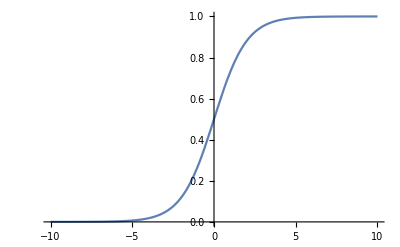

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
g[x_,c_]:=f[x+c]-f[x-c]
```

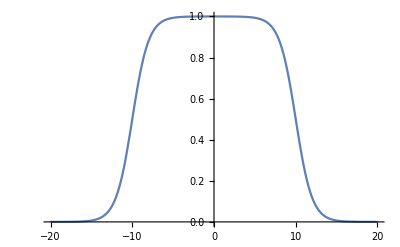

```mathematica
Plot[g[x,10],{x,-20,20}]
```

```mathematica
Plot3D[g[x-2,6]+g[y,10],{x,-20,20},{y,-20,20}]
```

-Graphics3D-

```mathematica
h[x_,y_]:=f[6(g[x-2,6]+g[y,10]-1.5)]
```

```mathematica
Plot3D[h[x,y],{x,-20,20},{y,-20,20},PlotRange-> All]
```

-Graphics3D-